```mathematica
SetDirectory[NotebookDirectory[]]
Get["Package.m"]
```

C:\Users\Simone\Documents\GitHub\MathematicaPrjMAS

# Rappresentazione Grafica delle Funzioni -Graphics- >< Versione Studente ><

## a cura di

Simone Bertolini, Alessio Francesconi, Matteo Grillini

## 1.1 Introduzione

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

Item duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

Subitem nam liber tempor cum soluta nobis eleifend option congue nihil imperdiet doming id quod mazim placerat facer possim assum.

Subitem typi non habent claritatem insitam; est usus legentis in is qui facit eorum claritatem.

### Equazioni di 1° Grado (Rette)

Teoria

Esercizi

### Equazioni di 2° Grado (Parabole)

Teoria

Esercizi

### Equazioni di 3° Grado

Teoria

Esercizi

Equazioni di 1 °Grado

### Introduzione

Conosciamo la forma delle funzioni di primo grado : f (x) = m X + q ma cosa vogliono dire i parametri m e q?

Ma soprattutto non ti ricorda la forma della retta?

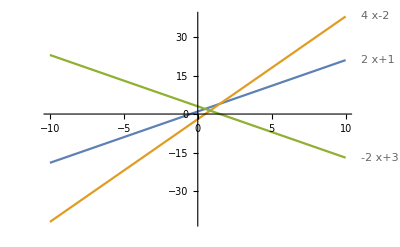

```mathematica
Plot[{2x+1,4x-2,-2x+3}, {x,-10,10},PlotLabels->"Expressions"]
```

### Comprensione guidata del parametro Q

Partiamo cercando di capire cosa rappresenta il q della formula nei grafici :

```mathematica
Manipulate[Plot[2*x+ q ,{x,-3, +3}, PlotRange-> zoom,PlotLabel-> 2x+q],{q, -10,+10},{zoom,10,1000}]
```

```mathematica
EventHandler[MouseAppearance[Style["Hai dubbi su come cambia il grafico quando cambia q?",FontColor->Blue],LinkHand],{"MouseClicked":>  MessageDialog["Il termine noto q indica l’ordinata del punto di intersezione del grafico con l’asse Y"]}]
```

Hai dubbi su come cambia il grafico quando cambia q?

### Comprensione del caso particolare

```mathematica
p1 = 0
```

0

Hai posto attenzione a cosa succede quando q = 0?

No

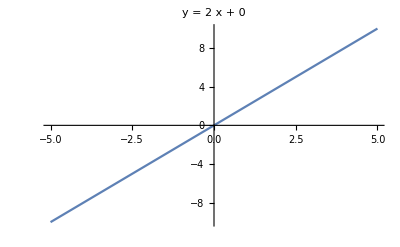

```mathematica
Row[{Hyperlink[StatusArea[Button["Si"], "AG_C1_G1"],{EvaluationNotebook[], "AG_C1_G1"}],"\t",Button["No",If[p1== 0,p1=1;Print[Plot[2x, {x,-5,+5}, PlotLabel->"y = 2 x + 0"]]]]}]
```

### Analisi guidata del coefficiente di primo grado

Ora abbiamo capito cosa vuol dire il termine noto sul grafico ma il coefficiente di primo grado m come si traduce sul grafico?

```mathematica
Manipulate[Plot[m*x+-2 ,{x,-3, +3}, PlotRange-> zoom,PlotLabel-> m x-2],{m, -10,+10},{zoom,10,1000}]
```

```mathematica
EventHandler[MouseAppearance[Style["Hai dubbi su come cambia il grafico quando cambia m?” ",FontColor->Blue],LinkHand],{"MouseClicked":>  MessageDialog["Il coefficiente di primo grado indica l’inclinazione del grafico rispetto all’asse X"]}]
```

Hai dubbi su come cambia il grafico quando cambia m?”

### Comprensione del caso particolare

```mathematica
p2=0
```

0

Hai notato cosa cambia se m < 0 o m > 0?

```mathematica
Row[{Button["Si"],"\t",Button["No",If[p2 == 0,p2=1;Print[Plot[{-x+2,x+2}, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere i grafici formano con l’asse X angoli acuti se m>0 e ottusi se m<0"],p2=1]]}]
```

Si	No

### Comprensione del caso particolare

```mathematica
p3=0
```

0

Hai notato cosa succede se m = 0?

```mathematica
Row[{Button["Si" ],"\t",Button["No",If[p3 == 0,p3=1;Print[Plot[0x+1, {x,-5,+5}, PlotLegends->"Expressions"]]; Print["Come puoi vedere il grafico è parallelo all'asse X"],p3=1]]}]
```

Si	No

### Caso particolare X=k

```mathematica
p4=0
```

0

Prima di farti sperimentare liberamente bisogna riflettere su un caso unico delle rette non delle funzioni.
Pensa a quale possa essere e poi scopriamolo insieme.


Il caso delle rette verticali che sono della forma X=k con k che è un qualunque numero.

```mathematica
Manipulate[ListLinePlot[{{k,10},{k,-10}},PlotRange->{{-4,+4},{-4,+4}},PlotLabel->StringJoin["x = ",ToString[k]]],{k,-3.5,3.5}]
```

### Ora tocca a te!

Inserisci tu le rette e osserva come sono rappresentate graficamente.Puoi confrontare contemporaneamente 5 equazioni

```mathematica
freeEq = {}
```

{}

```mathematica
currentEq =""
```

```mathematica
Dynamic[freeEq]
```

```mathematica
Panel[Column[{
Row[{InputField[Dynamic[currentEq],String],Button["Confronta",If[Length[freeEq]<5,AppendTo[freeEq,ToExpression[currentEq]],MessageDialog["Hai già inserito 5 grafici, eliminane uno prima di aggiungerne uno nuovo!"]]]}],Dynamic[Row[Table[With[{i=i},Column[{Plot[freeEq[[i]],{x,-10,+10},PlotLabel->ToString[freeEq[[i]]],ImageSize->Small],"\t",Button["Elimina",freeEq=Delete[freeEq,Position[freeEq,freeEq[[i]]]]]}]],{i,Length[freeEq]}]]]}]]
```

Confronta

### Esercizi

```mathematica
teacherEQ = {} (* Exercises solutions list *)
```

{}

```mathematica
{}

correctAnswer = 0
```

{}

0

```mathematica
teacherEQ = ReadList["g1.txt"] (* Loading teacher's file *)
```

ReadList::noopen: Cannot open g1.txt.

$Failed

```mathematica
If[Length[teacherEQ]=== 0, teacherEQ= {1+ x, 2 + 2x, 3 + 3x}]
```

{1+x,2+2 x,3+3 x}

```mathematica
If[Length[teacherEQ]<3,For[i=0,i<3-Length[teacherEQ],i++,AppendTo[teacherEQ,x*RandomInteger[{-10,+10}]+RandomInteger[{-10,+10}]]]](* Random function generation: This function complete the excercises list adding Random ones till minimum number is reached *)
```

```mathematica
Dynamic[teacherEQ]
```

```mathematica
exercises = {};
For[i=1,i<=Length[teacherEQ],i++,
sol={};
AppendTo[sol,teacherEQ[[i]]];(* Add correct answer *)
coeff = CoefficientList[teacherEQ[[i]],x];(* Get coefficients from expression i *)
 AppendTo[sol,coeff[[1]]-x*coeff[[2]]];(* Add y=-mx+q *)
AppendTo[sol,RandomInteger[{-10,10}]+x*RandomInteger[{-10,10}]];(* Add y=RND x + RND *)
AppendTo[sol,RandomInteger[{-10,10}]+x*coeff[[2]]];(* Add y=mx + RND *)
AppendTo[exercises,sol](* Add exercise to exercises list *)
]
```

```mathematica
Dynamic[exercises]
```

```mathematica
eq= RandomChoice[teacherEQ, 1](* Choice Random Function from a list*)
```

{3+3 x}

```mathematica
index = Position[teacherEQ, eq[[1]]] (* Get Index of Function from a list for append the response *)
```

{{2}}

```mathematica
ind = index [[1]] (* Get Integer *)
```

{2}

```mathematica
eq2= RandomChoice[teacherEQ, 1] (* Choice second Random function from a list*)
```

{2+x}

```mathematica
While[eq ==  eq2,Print[eq2]; eq2 = RandomChoice[teacherEQ,1]] (* Control that two function is different, if its isn t loop until it is*)
```

```mathematica
eq2
```

{-5-5 x}

```mathematica
{-5-5 x}
```

```mathematica
index = Position[teacherEQ, eq2[[1]]] (* Get Index of 2 Function from a list for append the response*)
```

{{1}}

```mathematica
ind2 = index [[1]](* Get Integer of Index*)
```

{1}

```mathematica
eq3= RandomChoice[teacherEQ, 1](* Choice Random Function from a list*)
```

{5+5 x}

```mathematica
While[eq3==  eq2 || eq3 == eq,Print[eq3]; eq3 = RandomChoice[teacherEQ,1]](* Control that two function is different, if its isn t loop until it is*)
```

```mathematica
eq3
```

eq3

```mathematica
index = Position[teacherEQ, eq3[[1]]] (* Get index for append response*)
```

{{3}}

```mathematica
ind3 = index [[1]](* Get Integer *)
```

{3}

```mathematica
answer = 0 (* Flag for count answer and control question *)
```

0

```mathematica
s2=0  (* User Variable Response 2*)
```

0

```mathematica
s3=0 (* User Variable Response 3*)
```

0

```mathematica
s1 = 0;(* User choise variable *)
en1 = True;(* Form enabling variable *)
(* Dynamic Load Plot Function Teacher and relative Answer, switched over answer*)
Dynamic[
If [answer === 0,Panel[Column[{Plot[eq,{x,-10,10},ImageSize->Large,PlotLabel->"A quale funzione corrisponde la seguente retta?"]RadioButtonBar[Dynamic[s1],RandomSample[exercises[[ind[[1]]]]]]}]], If[answer=== 1,Panel[Column[{Plot[eq2,{x,-10,10},ImageSize->Large,PlotLabel->"A quale funzione corrisponde la seguente retta?"],RadioButtonBar[Dynamic[s2],RandomSample[exercises[[ind2[[1]]]]]]}]]]Panel[Column[{Plot[eq3,{x,-10,10},ImageSize->Large,PlotLabel->"A quale funzione corrisponde la seguente retta?"],RadioButtonBar[Dynamic[s3],RandomSample[exercises[[ind3[[1]]]]]]}], Enabled->Dynamic[en1]]]]
```

```mathematica
Button["Verifica",If[answer===0,
	If[s1 === teacherEQ[[ind[[1]]]],
			correctAnswer++; MessageDialog["Risposta corretta"];answer++,
			If[s1=== 0,MessageDialog["Rispondi Prima di verificare"], 
			answer++;MessageDialog["Risposta errata, la soluzione corretta è :"eq[[1]]]]
	],
If[answer=== 1,
	If[s2 === teacherEQ[[ind2[[1]]]],
			correctAnswer++; MessageDialog["Risposta corretta"];answer++,
			If[s2=== 0,MessageDialog["Rispondi Prima di verificare"], 
			answer++;MessageDialog["Risposta errata, la soluzione corretta è :"eq2[[1]]]]
	],
If[answer=== 2,
	If[s3 === teacherEQ[[ind3[[1]]]],
			correctAnswer++; en1=False;MessageDialog["Risposta corretta"];answer++,
			If[s3=== 0,MessageDialog["Rispondi Prima di verificare"], 
			answer++;en1=False;MessageDialog["Risposta errata, la soluzione corretta è :"eq3[[1]]]]

]]]
]]
(* Button that checks if the answer is correct and it blocks user interaction *)
```

Verifica

```mathematica
Dynamic[answer]
```

```mathematica
Dynamic[correctAnswer]
```

```mathematica
(* Button Hyperlink control if all question are answer, else block user *)
```

```mathematica
Dynamic[If[answer===  3,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RF_G1"],{EvaluationNotebook[], "RF_G1"}], "Rispondi e Verifica la risposta prima di passare alla prossima sezione"]]
```

### Esercizi Riconoscimento Grafico

```mathematica
enab = True;(*Enable Response after first choice*)
```

```mathematica
ans=0 (* User Variable Choice*)
```

0

```mathematica
s1 = 0
```

0

```mathematica
listFunction = RandomSample[exercises[[ind[[1]]]]](* Order Random the list of function*)
```

{2-2 x,2+2 x,10+2 x,5-8 x}

```mathematica
Normal[CoefficientArrays[listFunction,{x}]⟦2⟧]
```

{{-2},{2},{2},{-8}}

```mathematica
(* Plot all function with relative checkbox for answer and append 'label' function *)
```

{a quale grafico corrisponde la funzione (2+2 x)}

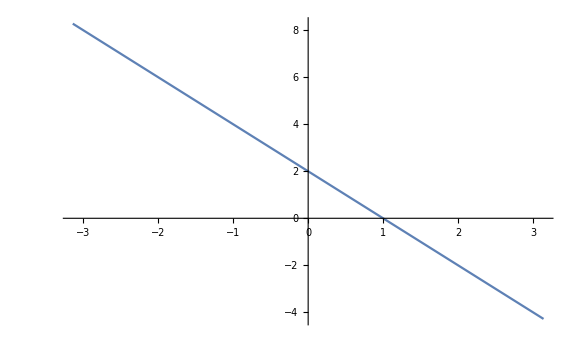
| 1 -Graphics-

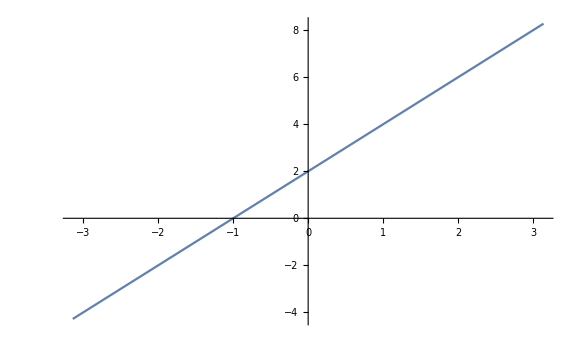
| 2 -Graphics-

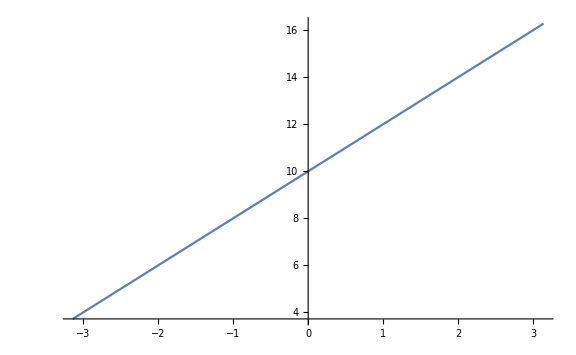
| 3 -Graphics-

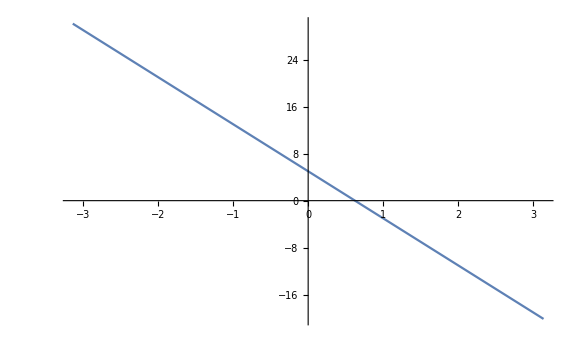
| 4 -Graphics-

```mathematica
Panel["a quale grafico corrisponde la funzione" eq]
For[i=1,i≤ Length[listFunction],i++,Print[Plot[listFunction[[i]],{x,-Pi,Pi}, ImageSize->Large]CheckboxBar[Dynamic[s1],{listFunction[[i]]->i}, Enabled->Dynamic[enab]]]]
```

```mathematica
Button["Verifica",
	If[s1 [[1]]=== teacherEQ[[ind[[1]]]],
			enab = False; correctAnswer++; MessageDialog["Risposta corretta"];ans++,
			If[s1=== 0,MessageDialog["Rispondi Prima di verificare"], 
			ans++;enab= False;MessageDialog["Risposta errata, la soluzione corretta è :"eq[[1]]]]
	]]
```

Verifica

```mathematica
(* Button Verify Response, if not insert alert, else say if it is corret or wrong*)
```

```mathematica
Dynamic[If[ans >=  1,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RF_G1_1"],{EvaluationNotebook[], "RF_G1_1"}], "Rispondi e Verifica la risposta prima di passare alla prossima sezione"]]
(* Button Verify Response, if not insert block user, else button with hyperlink*)
```

```mathematica
Esercizio Riconoscere Grafico 2
```

```mathematica
enab2 = True;(* Enable Response after first Choise*)
```

```mathematica
s2 =0 (* User Choice Variable*)
```

0

```mathematica
(* Order Random List Function*)
```

```mathematica
listFunction2 = RandomSample[exercises[[ind2[[1]]]]]
```

{-5-5 x,-5+5 x,6-5 x,-9+2 x}

{a quale grafico corrisponde la funzione (-5-5 x)}

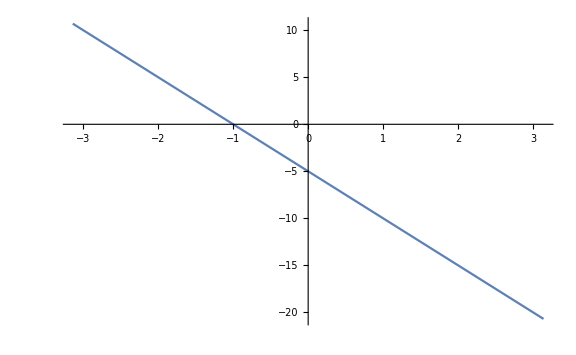
| 1 -Graphics-

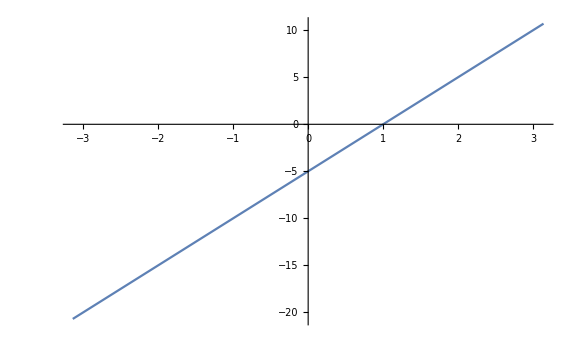
| 2 -Graphics-

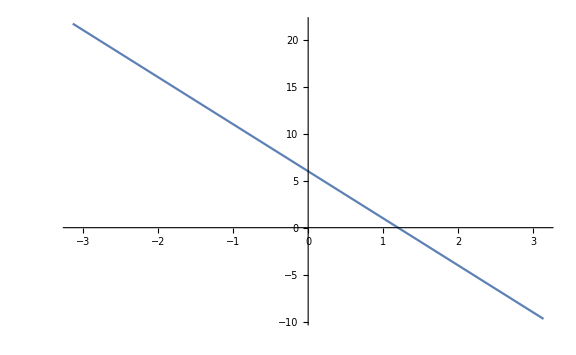
| 3 -Graphics-

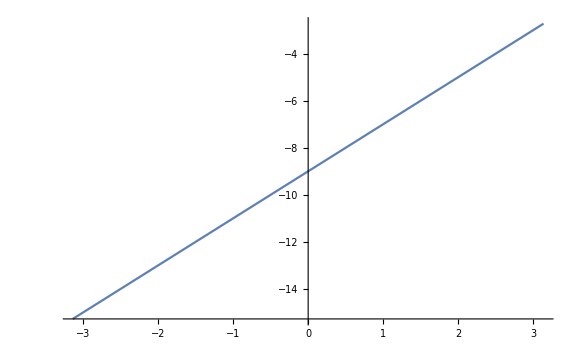
| 4 -Graphics-

```mathematica
(* Plot all function of list with relative checkbox to select*)
Panel["a quale grafico corrisponde la funzione" eq2]
For[i=1,i≤ Length[listFunction2],i++,Print[Plot[listFunction2[[i]],{x,-Pi,Pi}, ImageSize->Large]CheckboxBar[Dynamic[s2],{listFunction2[[i]]->i}, Enabled->Dynamic[enab2]]]]
```

```mathematica
Button["Verifica",
	If[s2 [[1]]=== teacherEQ[[ind2[[1]]]],
			enab2 = False; correctAnswer++; MessageDialog["Risposta corretta"];ans++,
			If[s2 === 0,MessageDialog["Rispondi Prima di verificare"], 
			ans++;enab2= False;MessageDialog["Risposta errata"]]
	]]
```

```mathematica
"Verifica"
(* Button Verify Response, if not insert alert, else say if it is corret or wrong*)
```

```mathematica
Dynamic[If[ans ≥   2,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"RF_G1_2"],{EvaluationNotebook[], "RF_G1_2"}], "Rispondi e Verifica la risposta prima di passare alla prossima sezione"]]
(* Button Verify Response, if not insert block user, else button with Hyperlink*)
```

Esercizio Riconoscere Grafico 3

```mathematica
enab3 = True;(* Enable Response after first Choice *)
```

```mathematica
s3= 0 (* User Variable Choice*)
```

0

```mathematica
listFunction3= RandomSample[exercises[[ind3[[1]]]]] (* Order Random List Function*)
```

{3-7 x,1+x,4+x,1-x}

{a quale grafico corrisponde la funzione (1+x)}

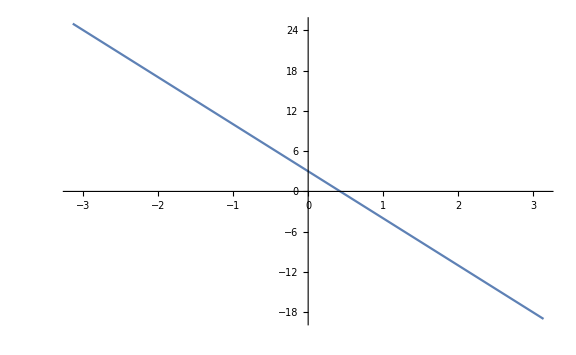
| 1 -Graphics-

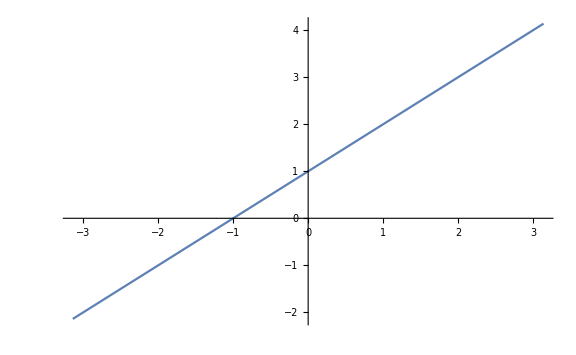
| 2 -Graphics-

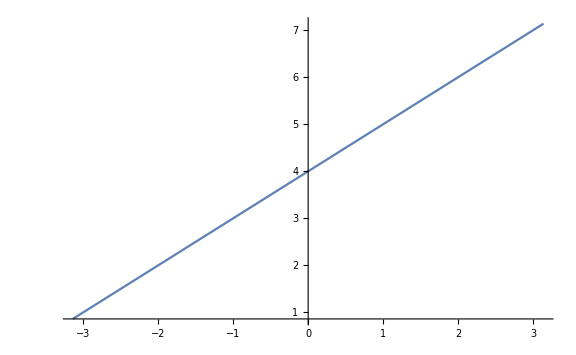
| 3 -Graphics-

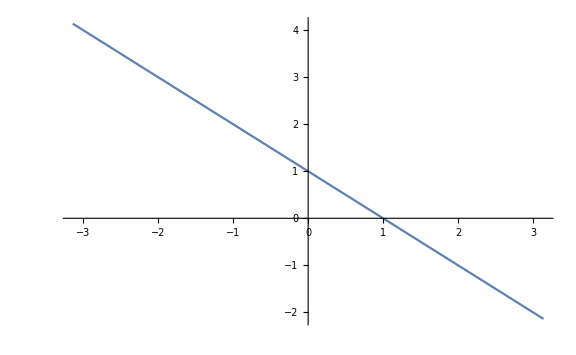
| 4 -Graphics-

```mathematica
(* Plot all function with relative checkbot for response*)
Panel["a quale grafico corrisponde la funzione" eq3]
For[i=1,i≤ Length[listFunction3],i++,Print[Plot[listFunction3[[i]],{x,-Pi,Pi}, ImageSize->Large]CheckboxBar[Dynamic[s3],{listFunction3[[i]]->i}, Enabled->Dynamic[enab3]]]]
```

```mathematica
(* Button Verify Response, if not insert alert, else say if it is corret or wrong*)
Button["Verifica",
	If[s3 [[1]]=== teacherEQ[[ind3[[1]]]],
			enab3 = False; correctAnswer++; MessageDialog["Risposta corretta"];ans++,
			If[s3 === 0,MessageDialog["Rispondi Prima di verificare"], 
			ans++;enab3= False;MessageDialog["Risposta errata"]]
	]]
```

Verifica

```mathematica
(* Button Verify Response, if not insert block user, else button with hyperlink*)
Dynamic[If[ans===  3,Hyperlink[StatusArea[Button["Vai alla prossima sezione"],"E_2G"],{EvaluationNotebook[], "E_2G"}], "Rispondi e Verifica la risposta prima di passare alla prossima sezione"]]
```

Equazioni di 2 °Grado

### Introduzione

```mathematica
Manipulate[Plot[a*x^2+b*x + q ,{x,-3, +3}, PlotRange-> zoom],{a,-10, +10},{b,-10, +10},{q, -10,+10},{zoom,10,1000}]
```

```mathematica
list2 = {}
```

{}

```mathematica
DynamicModule[{f},
Column[
{
Panel[

Row[
{
InputField[
Dynamic[a],Number,FieldSize->Full
],
Style["x^2 + ",12],
InputField[
Dynamic[b],Number,FieldSize->Full
],
Style["x + ",12],
InputField[
Dynamic[q],Number,FieldSize->Full
]
}
]
],
Dynamic@Refresh[f=a*x^2+b*x+ q; "", TrackedSymbols:>{a,b,q}]
Button[
"Add",
If[a== Null ||b== Null || q==Null || a== 0,
MessageDialog["Alcuni campi inseriti non sono corretti!"],
AppendTo[
list2,
f
],
AppendTo[
list2,
f
]
]
] 
}
]
]
```

```mathematica
Dynamic[list2]
```

```mathematica
Dynamic[Plot[list2,{x, -10,10}]]
```

```mathematica
Button[
"Delete",
list2= {}]
```

Delete

Equazioni di 3 °Grado

### Introduzione

```mathematica
Manipulate[Plot[a*x^3+b*x ^2+c*x+ q ,{x,-3, +3}, PlotRange-> zoom],{a,-10, +10},{b,-10, +10},{c,-10,+10},{q, -10,+10},{zoom,10,1000}]
```

```mathematica
list3={}
```

{}

```mathematica
DynamicModule[{f},
Column[
{
Panel[

Row[
{
InputField[
Dynamic[a],Number,FieldSize->Full
],
Style["x^3 + ",12],
InputField[
Dynamic[b],Number,FieldSize->Full
],
Style["x^2 + ",12],
InputField[
Dynamic[c],Number,FieldSize->Full
],
Style["x + ",12],
InputField[
Dynamic[q],Number,FieldSize->Full
]
}
]
],
Dynamic@Refresh[f=a*x^3+b*x^2+c*x + q; "", TrackedSymbols:>{a,b,c,q}]
Button[
"Add",
If[a== Null ||b== Null || c== Null||q==Null || a== 0,
MessageDialog["Alcuni campi inseriti non sono corretti!"],
AppendTo[
list3,
f
],
AppendTo[
list3,
f
]
]
] 
}
]
]
```

```mathematica
Dynamic[list3]
```

```mathematica
Dynamic[Plot[list3,{x,-10, 10}]]
```

```mathematica
Button[
"Delete",
list3= {}]
```

Delete

```mathematica
DialogNotebook[Column[{"The changes have been saved.",DefaultButton[]}]]
```

The changes have been saved.

```mathematica
inputSqrt = "x+1"
```

x+1

```mathematica
Button["√x",
CreateDialog[
Column[
{"Insert Value of Sqrt",InputField[
Dynamic[inputSqrt],String,FieldSize->Full
],DefaultButton[]}
]
]
]
```

√x

```mathematica
Dynamic[inputSqrt]
```

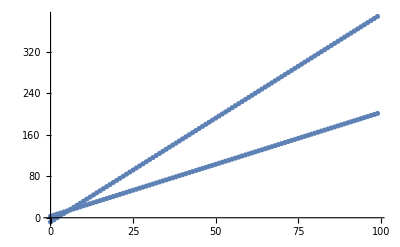

```mathematica
v1={};v2={};
For[t=0,t<100,t=t+1,y=2 t+3;
z=4 t-8;
AppendTo[v1,{t,y}];
AppendTo[v2,{t,z}];]

Show[{ListPlot[v1],ListPlot[v2]},PlotRange->All]
```

```mathematica
Hyperlink[StatusArea["click me","AG_C1_G1"],{EvaluationNotebook[],"AG_C1_G1"}]
```